```mathematica
nMatrix= Import[NotebookDirectory[]<>"n2D.mat"]⟦1⟧;
avgEnergy = Import[NotebookDirectory[] <> "../saved_outputs/avgEnergy.mat"]⟦1⟧;
Dimensions@nMatrix;
nMatrix=Transpose[nMatrix,{1,4,2,3}];
{frames,X,Y}=Dimensions[nMatrix]⟦;;-2⟧
θMatrix=ArcTan[nMatrix⟦;;,;;,;;,1⟧,nMatrix⟦;;,;;,;;,2⟧];
```

{50,10,10}

```mathematica
Manipulate[ListVectorPlot[nMatrix⟦frame,;;,;;⟧,VectorStyle-> Blue,VectorPoints->All],{frame,1,frames,1}]
```

```mathematica
(*Manipulate[ListDensityPlot[Sin[θMatrix⟦frame⟧]^2 ᵀ,ColorFunctionScaling->False,ColorFunction->GrayLevel],{frame,1,frames,1}]*)
```

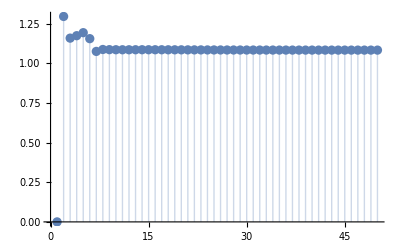

```mathematica
ListPlot[avgEnergy, PlotRange->All,Filling->Axis]
```

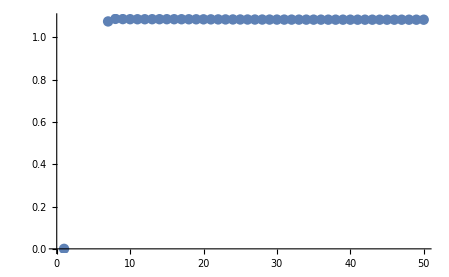

```mathematica
ListPlot[{0.,1.2965761061742789,1.1598023488870153,1.175175211348111,1.194206914453935,1.156482330919994,1.076011731887819,1.088086218563446,1.0870596625087101,1.0865999677531708,1.0863953280048886,1.0864144761650822,1.0865187783514767,1.0865908918821618,1.0865913237932483,1.0865277681747068,1.086419425144511,1.0862826756702963,1.0861295329366771,1.0859694190600566,1.0858088786198992,1.0856527851539253,1.0855042861550421,1.0853657932359448,1.085238162373206,1.0851215601946615,1.085016063786419,1.084920991843714,1.0848355318847587,1.0847590974054513,1.0846907683360467,1.0846297610480138,1.0845752774961244,1.0845267740404458,1.084483565161948,1.084445051034703,1.0844108256487517,1.0843803900181,1.084353309613212,1.0843292881548598,1.0843079651924856,1.084289026746915,1.0842722566283556,1.0842573949341976,1.0842442307400055,1.0842325617527413,1.0842222474718717,1.084213121884689,1.084205041137634,1.0841979050128812}, PlotRange->All]
```

```mathematica
avgEnergy
```

{{0.,1.29658,1.1598,1.17518,1.19421,1.15648,1.07601,1.08809,1.08706,1.0866,1.0864,1.08641,1.08652,1.08659,1.08659,1.08653,1.08642,1.08628,1.08613,1.08597,1.08581,1.08565,1.0855,1.08537,1.08524,1.08512,1.08502,1.08492,1.08484,1.08476,1.08469,1.08463,1.08458,1.08453,1.08448,1.08445,1.08441,1.08438,1.08435,1.08433,1.08431,1.08429,1.08427,1.08426,1.08424,1.08423,1.08422,1.08421,1.08421,1.0842}}